Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 5. DERIVADAS. NOTAS Y PRÁCTICAS.

## Funciones reales. Derivadas. (Para recordar)

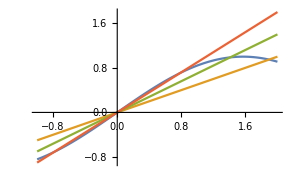
Para el estudio del cambio de una función, f, podríamos considerar cómo varía f entre un punto y otro, f(x)-f(x_0). Sin embargo, este dato no es significativo si no tenemos en cuenta la distancia, o diferencia, entre x y x_0.

La expresión (f(x)-f(x_0))/(x-x_0)  se llama cociente incremental o tasa de variación media de la función f en el intervalo de extremos x y x_0.
Si existe el límite de  (f(x)-f(x_0))/(x-x_0) cuando x tiende a x_0, la función se dice derivable en el punto x_0 y el valor del límite es la derivada de f en x_0. Se denota f’(x_0).

Si consideramos límites laterales podríamos hablar de derivadas laterales. 

Desde el punto de vista geométrico podríamos ver el cociente incremental como la pendiente de la recta secante a la gráfica de la función f, pasando por los puntos (x_0,f(x_0)) y (x,f(x)). Al acercarse los dos puntos, si la gráfica es “suave” y no tiene “picos”, la recta secante tiende a ser la recta tangente. Así, la ecuación de la recta tangente sería 
y=f(x_0) + f ’(x_0) (x-x_0). La ecuación de la recta normal sería y=f(x_0)-(x-x_0)/f’(x_0).
							-Graphics-

La mayoría de las funciones que conocemos son derivables en todos los puntos. Quizás, la más conocida que tiene puntos de su dominio donde no es derivable podría ser la función valor absoluto, |x|, que no es derivable en el punto 0. Tampoco es derivable la función √x en el punto 0. Ejemplos de funciones derivables en todos los puntos de dominio son: sen x, cos x, ⅇ^x, log x, o los polinomios. Para calcular derivadas hay que conocer la derivadas de algunas funciones usuales:

f(x) | f'(x)
1 | 0
x | 1
x^n | n x^(-1+n)
e^x | e^x
log(x) | 1/x
a^x | a^x log(a)
sen(x) | cos(x)
cos(x) | -sen(x)
arctg(x) | 1/(1+x^2)
√x | 1/(2 √x)

También, debemos conocer que la suma, resta, producto, cociente y composición de funciones derivables también es derivable. Además,

1) (c f)‘ (x_0)= c f ’(x_0), para cualquier constante c. 
2) (f+g)’(x_0) = f ’(x_0) + g ’(x_0)
3) (f-g)’(x_0) = f ‘(x_0) - g ‘(x_0)
4) (f g)’(x_0) = f ‘(x_0)g(x_0) + f(x_0)g ‘(x_0)
5) (f/g)’ (x_0) = (f '(x_0)g(x_0) - f(x_0)g '(x_0))/(g(x_0))^2
6) (f ∘ g)’ (x_0) = f ’(g(x_0)) g’(x_0)

Aplicaciones de la derivada.

Teorema. Si f:(a,b)→ℝ tiene un máximo o un mínimo relativo en un punto interior x_0 ∈ (a,b) y es derivable en x_0, entonces f ’(x_0)=0.

(Aunque no es suficiente que la derivada sea cero para que haya un máximo o mínimo relativo. Por ejemplo, f(x)= x^3, en el punto x=0 no tiene máximo ni mínimo relativo, aunque se anula la derivada.)

Teorema de Rolle. Si f:[a.b]→ℝ es continua y derivable, y f(a)=f(b), entonce existe un punto c en (a,b) tal que f ’(c)=0.

Como consecuencia:
Si una función tiene n raíces reales distintas en el intervalo [a,b], la función derivada tiene al menos n-1 raíces reales distintas en (a,b)).

O también:
Si f ’ tiene solo n raíces reales en (a,b), entonces f tiene a lo sumo n+1 raíces reales distintas en [a,b].

Derivadas y crecimiento de funciones
Si f ’(x)=0 en todo punto de un intervalo (a,b), entonces f es constante en (a,b).
Recíprocamente, si f es constante en (a,b), entonces f’(x)=0 en (a,b).

Si f ‘(x)≥0 en todo punto de un intervalo (a,b), entonces f es creciente en (a,b).
Recíprocamente, si f es derivable y creciente en (a,b), entonces f’(x)≥0 en todo el intervalo (a,b).

Si f ‘(x)>0 en todo punto de un intervalo (a,b), entonces f es estrictamente creciente en (a,b).
Sin embargo, si f es derivable y estrictamente creciente en (a,b), no puede asegurarse que f’(x)>0 en (a,b). La función x^3 es estrictamente creciente pero el el punto 0 su derivada es 0. 

Análogamente:
Si f ‘(x)≤0 en todo punto de un intervalo (a,b), entonces f es decreciente en (a,b). 
Recíprocamente, si f es derivable y decreciente en (a,b), entonces f’(x)≤0 en (a,b).  

Si f ‘(x)<0 en todo punto de un intervalo (a,b), entonces f es estrictamente decreciente en (a,b). 
Sin embargo, si f es derivable y estrictamente decreciente en (a,b), no puede asegurarse que f’(x)<0 en (a,b). La función -x^3 es estrictamente decreciente pero el el punto 0 su derivada es 0.

Derivada y convexidad de funciones
Si f’’(x)≥0 en todo punto de un intervalo (a,b), entonces f es convexa (∪) en (a,b).
Si f’’(x)≤0 en todo punto de un intervalo (a,b), entonces f es cóncava (∩) en (a,b).

Hay libros y profesores que definen la convexidad y concavidad justo al contrario. Lo importante es saber que cuando la función cumple que f’’(x)≥0 en todo punto de un intervalo (a,b), entonces f tiene la forma de ∪ en (a,b). Dicho de otra forma, que si f’’(x)=(f’)’(x)≥0, la derivada primera es una función creciente y que la recta tangente cada vez tendrá una pendiente mayor.

Las funciones convexas son aquellas que al considerar la recta que pasa por dos puntos de su gráfica, la función es mayor o igual que la recta antes del primer punto y después del segundo, siendo menor o igual que la recta entre los dos puntos.

Regla de L’Hôpital 
Si f y g son dos funciones son derivables en (a,b) con -∞≤a<b≤∞, con g’(x)≠ 0 en (a,b), si
lím_(x→ a) f(x) = lím_(x→ a) g(x) = 0, entonces si existe lím_(x→a) (f'(x))/(g'(x))  entonces también existe el lím_(x→ a) (f(x))/(g(x)) y son iguales.
También puede aplicarse para el punto b, o cuando el límite de g es infinito.

Hay que tener cuidado con las conclusiones si no existe el lím_(x→a) (f'(x))/(g'(x)). Por ejemplo, si para calcular el límite lím_(x→∞) (x + cos x)/x aplicamos la Regla de L’Hôpital, nos encontramos que el límite   lím_(x→∞) (1 - sen x)/1 no existe. Sin embargo, el límite lím_(x→∞) (x + cos x)/x existe y vale 1. La cuestión es que no podemos calcularlo por la Regla de L’Hôpital. Para calcular este límite, podemos dividir numerador y denominador por x y obtenemos lím_(x→∞) (x + cos x)/x = lím_(x→∞) (x/x + (cos x)/x)/(x/x)= lím_(x→∞) (1 + (cos x)/x)/1= (1 + 0)/1= 1

Cálculo de máximos y mínimos absolutos de funciones continuas en intervalos cerrados y acotados.
Si f:[a.b]→ℝ es continua, por el teorema de Weierstrass sabemos que tendrá máximo y mínimo absolutos. Los máximos y mínimo pueden estar en el interior o en lo extremos del intervalo. Si están en el interior y la función es derivable en ellos, la derivada debe ser cero.  De aquí que para encontrarlos, los pasos a seguir son:
1) Encontrar los puntos donde f ’(x)=0.
2) Considerar los puntos donde no exista la derivada de f.
3) Considerar los extremos del intervalo, a y b.
4) Evaluar la función f en los puntos encontrados en los 3 pasos anteriores. Encontrar los máximos y mínimos absolutos de f.

## Cálculos con el Mathematica

Para calcular derivadas, podemos colocar la prima ' (la que está junto al 0) una o varias veces o podemos utilizar la función D. Podemos calcular la función derivada o la derivada de una función en un punto.

```mathematica
f[x_]:= Sin[x]
```

```mathematica
f'[x]
```

Cos[x]

```mathematica
f'[0]
```

1

```mathematica
f''''[x]
```

Sin[x]

Para derivadas de orden superior, puede ser más sencillo usar la función D. Por ejemplo, para calcular la derivada 20,

```mathematica
D[f[x],{x,20}]
```

Sin[x]

```mathematica
D[x ⅇ^x,{x,20}]
```

20 ⅇ^x+ⅇ^x x

Para evaluar las derivadas en un punto, podemos usar:

```mathematica
f'''[0]
```

-1

```mathematica
D[f[x],{x,3}]/.x->0
```

-1

Pero hay que tener cuidado con no hacer

```mathematica
D[f[0],{x,3}]
```

0

Pues f[0] es una constante, y sus derivadas serán siempre cero.

Comprobar derivadas hechas a mano

Cuando hayamos calculado a mano la derivada de una función y queramos comprobar si están bien los cálculos, podemos pedir al Mathematica que calcule la derivada. En el caso de que ambos cálculos presenten aspectos diferentes podemos pedir que compare ambas expresiones, poniendo doble igual (incluso pidiendo que simplifique).

```mathematica
D[Sin[x]/Cos[x],{x,1}]
```

Sec[x]^2

```mathematica
Sec[x]^2== (Cos[x]^2+Sin[x]^2)/Cos[x]^2
```

Sec[x]^2==Sec[x]^2 (Cos[x]^2+Sin[x]^2)

```mathematica
Sec[x]^2== (Cos[x]^2+Sin[x]^2)/Cos[x]^2//Simplify
```

True

Derivación implícita

Para derivadas implícitas, escribimos la expresión especificando en este caso que y depende de x.

```mathematica
D[x^2+y[x]^2==1 ,x]
```

2 x+2 y[x] y'[x]==0

Recta Tangente

Para calcular la recta tangente en un punto, evaluamos la función y la derivada. 
La ecuación de la recta tangente es y = f(x_0) + f ’(x_0)(x-x_0). Las funciones f(x) y f(x_0) + f ‘(x_0)(x-x_0) coinciden en el punto x_0 y tienen la misma pendiente, por ello sus gráficas son tangentes.

```mathematica
f[x_]:= E^x Cos[x]
```

```mathematica
f[0]+f'[0](x-0)
```

1+x

```mathematica
r[x_]:=1+x
```

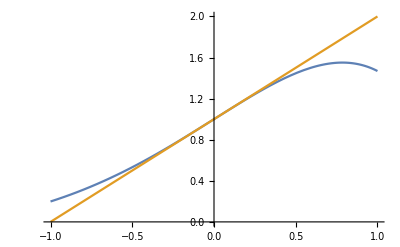

```mathematica
Plot[{f[x],r[x]},{x,-1,1}]
```

La recta tangente nos permite tener una aproximación de los valores de la función en puntos cercanos al punto de tangencia. 
Para evaluar la función f(x) cerca del punto 0, podemos evaluar la recta tangente.

```mathematica
{f[0.123],r[0.123],f[0.123]-r[0.123]}
```

{1.12234,1.123,-0.000659375}

```mathematica
{f[0.0583],r[0.0583],f[0.0583]-r[0.0583]}
```

{1.05823,1.0583,-0.0000679996}

```mathematica
{f[-0.13],r[-0.13],f[-0.13]-r[-0.13]}
```

{0.870686,0.87,0.000685968}

Podemos comparar los valores de f y de la recta tangente en puntos cercanos al 0 y ver las diferencias.

Recta Normal

Cálculo de la recta normal a la gráfica de la función. La recta tangente tenía ecuación 
			y=f(x_0)+f’(x_0)(x-x_0).
La recta normal es similar, cambia la pendiente, y=f(x_0)- (1/f’(x_0))(x-x_0)

```mathematica
h[x_]:=ⅇ^x
```

```mathematica
t[x_]:=h[0]+h'[0]x
```

```mathematica
n[x_]:=h[0]-(1/h'[0])x
```

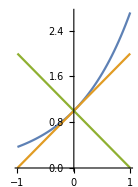

```mathematica
Plot[{h[x],t[x],n[x]},{x,-1,1},AspectRatio->Automatic]
```

## Estudio del signo de una función. Estudio del crecimiento y la convexidad de una función.

Consideramos la función f(x) = x^3 - 4x + 8. Se trata de un polinomio que está definido en toda la recta real, es continua y derivable tanta veces como deseemos.

```mathematica
f[x_]:= x^3-4x+8
```

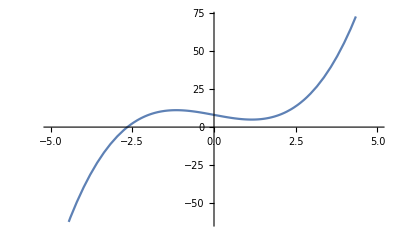

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
Solve[f[x]==0,x]//Simplify
```

{{x→((1-ⅈ √3) (18-2 √69)^(1/3)+(1+ⅈ √3) (2 (9+√69))^(1/3))/6^(2/3)},{x→((1+ⅈ √3) (18-2 √69)^(1/3)+(1-ⅈ √3) (2 (9+√69))^(1/3))/6^(2/3)},{x→-(2/3)^(2/3) ((9-√69)^(1/3)+(9+√69)^(1/3))}}

```mathematica
N[%]
```

{{x→1.32472+1.12456 ⅈ},{x→1.32472-1.12456 ⅈ},{x→-2.64944}}

La función f(x) se anula en el punto -2.64944, y dado que el dominio es toda la recta, debemos tomar un punto antes y otro después del -2.64944, por ejemplo -3 y 0.

```mathematica
{f[-3],f[0]}
```

{-7,8}

La función f es continua en toda la recta y sólo se anula en el -2.64944, por tanto tiene un sólo signo desde menos infinito hasta ese punto y un sólo signo desde ese punto hasta infinito. Como f en -3 es negativa, la función f será negativa en el intervalo (-∞, -2.6944). Como f en 0 es positiva, la función f será positiva en el intervalo (-2.6944, ∞).

De forma similar, procedemos para encontrar el signo de la derivada. La derivada es otra vez un polinomio, su dominio es toda la recta real. Llamamos g(x) a f’(x).

```mathematica
g[x_]:=f'[x]
```

```mathematica
Solve[g[x]==0,x]//Simplify
```

{{x→-2/(√3)},{x→2/(√3)}}

```mathematica
N[%]
```

{{x→-1.1547},{x→1.1547}}

Como la función derivada es también continua en toda la recta y se anula en los puntos - 1.1547 y 1.1547, debemos escoger un punto antes de -1.1547, otro entre ambos y otro después de 1.1547. Por ejemplo, podrían ser los puntos -2, 0 y 3. Evaluamos g en esos puntos.

```mathematica
{g[-2],g[0],g[3]}
```

{8,-4,23}

La función g es positiva en -2, por tanto lo será hasta -2/(√3), negativa en 0, por tanto será negativa entre -2/(√3) y 2/(√3), y positiva en 3, por tanto, g será  después de 2/(√3). Esto implica, que la función f  es creciente hasta -2/(√3), decreciente entre -2/(√3) y 2/(√3) y creciente después.
En -2/(√3) hay un máximo local y en 2/(√3) un mínimo local de f.

De forma similar, hacemos para estudiar los signos de f ’’.

```mathematica
h[x_]:=f''[x]
```

```mathematica
Solve[h[x]==0,x]//Simplify
```

{{x→0}}

```mathematica
N[%]
```

{{x→0.}}

Como la derivada segunda se anula en 0, y es continua en toda la recta, debemos tomar un punto antes del 0 y otro después del 0. Por ejemplo, -1 y 1.

```mathematica
{h[-1],h[1]}
```

{-6,6}

La función h es negativa hasta 0 y positiva después.
La función f ’ es decreciente hasta 0 y creciente después.
La función f   es cóncava hasta 0 y convexa después.
En 0 hay un cero de f ‘’, un mínimo de f ’ y un punto de inflexión de f.

## Cálculo de máximos y mínimos absolutos de una función continua en un intervalo cerrado y acotado.

Consideremos la función g(x)=√(|x|) definida en el intervalo [-2,3]. La función g es la composición de la función raíz cuadrada y la función valor absoluto. Estas funciones son continuas, por tanto la composición es continua y al ser el intervalo cerrado y acotado, la función tiene máximo y mínimo absolutos (Teorema de Weierstrass).

```mathematica
g[x_]:= Sqrt[Abs[x]]
```

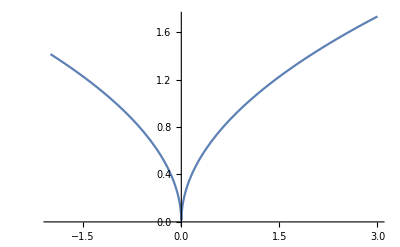

```mathematica
Plot[g[x],{x,-2,3}]
```

Los puntos candidatos son los extremos, los puntos donde la derivada se anula y los puntos donde la función no sea derivable.

```mathematica
Solve[g'[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→InverseFunction[Abs',1,1][0]}}

```mathematica
Solve[g'[x]==0,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Abs'[x]/(2 √Abs[x])==0,x,ℝ]

```mathematica
Reduce[g'[x]==0,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Abs'[x]/(2 √Abs[x])==0,x]

```mathematica
Reduce[g'[x]==0,x,Reals]
```

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

False

El Mathematica al usar Solve no nos da una información clara. Podemos usar también Reduce, y podemos precisar que deben ser soluciones reales.

Hacemos el estudio nosotros. 

La función g(x) vale √x cuando x sea mayor o igual que cero y vale √-x cuando x sea menor o igual a cero. 

La derivada será 1/(2 √x) cuando x sea mayor que 0 y -1/(2 √-x) cuando x sea menor que 0. Por tanto, tenemos que la derivada no se anula en el intervalo (-2,0), ni en el (0,3). En el punto 0, la función parece que no va a ser derivable (ni la función valor absoluto, ni la función raíz cuadrada son derivables en 0). La composición de funciones derivables es derivable, en el caso en que una de las dos no sea derivable, no es seguro que la composición tenga que ser no derivable. En cualquier caso, no suele traer cuenta estudiar la derivabilidad en 0, simplemente podemos añadir el punto 0 al conjunto de los puntos donde no hay derivada, y sólo tendremos que evaluar la función en un punto más.

Los puntos candidatos son los extremos (-2 y 3), los puntos donde la derivada se anula (ninguno) y donde la función no sea derivable (0, por si acaso). Evaluemos la función g.

```mathematica
{g[-2],g[3],g[0]}
```

{√2,√3,0}

```mathematica
N[%]
```

{1.41421,1.73205,0.}

El máximo está en (3, √3) y el mínimo en (0,0).

```mathematica
Plot[g[x],{x,-2,3}]
```

-Graphics-

## Problemas de optimización.

Consideremos dos rectángulos iguales de 200 de largo y 30 de ancho. Estudiemos con qué ángulo debemos colocarlos para que el volumen del prisma triangular que forman sea máximo.

```mathematica
Manipulate[ParametricPlot3D[{{0,200(1-s),0}t+(1-t){30Cos[a],200(1-s),30Sin[a]},{0,200(1-s),0}t+(1-t){-30Cos[a],200(1-s),30Sin[a]}},{t,0,1},{s,0,1}],{a,0,Pi/2}]
```

El prisma generará un volumen que será la superficie del triángulo multiplicada por la longitud (200). La superficie del triángulo está en función de la apertura que tengan los dos lados. Esta apertura podría expresarse en términos del ángulo que formen en el punto de unión, o de la distancia que haya entre los otros extremos, o de la altura. Según la variable que usemos encontraremos diferentes funciones con diferentes dominios. 

Usaremos como variable la distancia entre los extremos. Se trata de un triángulo isósceles, con dos lados de longitud 30. Si x es la separación, esta será la longitud de la base del triángulo. La altura del triángulo será la raíz cuadrada de 30 al cuadrado menos (x/2) al cuadrado. La superficie del triángulo será base por altura dividido por 2 y el volumen será v(x).

```mathematica
v[x_]:=100 x Sqrt[30^2-(x/2)^2]
```

El dominio de v, será el conjunto de valores admisibles para x. Como mínimo x valdría 0 y como máximo sería 60 (el doble de 30). La función es continua, por ser producto y composición de continuas. Por tanto, existen máximos y mínimos absolutos en el intervalo [0,60].

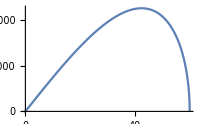

```mathematica
Plot[v[x],{x,0,60}]
```

```mathematica
Solve[v'[x]==0,x]
```

{{x→-30 √2},{x→30 √2}}

Los puntos candidatos serán los extremos del intervalo (0 y 60), los puntos donde se anula la derivada (sólo el 30√2, pues el otro está fuera del dominio) y los puntos donde la función no sea derivable (la función es derivable en todos los puntos del interior y los extremos ya son candidatos). Por tanto, evaluamos la función en 0, 60 y 30√2.

```mathematica
{v[30 √2],v[0],v[60]}
```

{90000,0,0}

El volumen máximo será 90000, y se consigue si los lados del triángulo son los 2 de 30 y el tercero es 30√2 . Puede verse que el ángulo que forman los dos rectángulos debe ser 90 grados.